#### 080118New Calibration trace at YOKO=0mA, 6.3~6.6GHz, 5dBm 10us integration 50Kavg,100KHz step

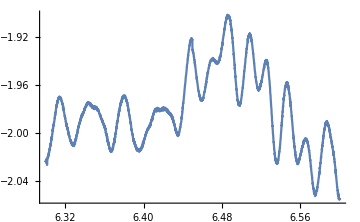
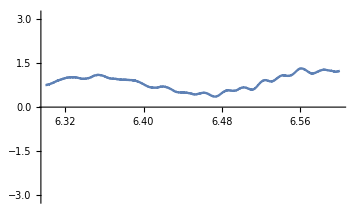

```mathematica
file="E:\\Data\\fluxonium waveguide\\one_tone_6.3GHz_to_6.6GHz_5dBm_0mA_10us integration_50Kavg_100KHz step_080118.dat";
data=Import[file];
header=Take[data,1];
ref=Drop[data,1];
edelay = 322.0;
ampref=ref[[;;,3]];
phaseref=ref[[;;,2]];
Row@{ListLinePlot[{#[[1]],Log10@#[[3]]}&/@ref,PlotRange->All,ImageSize->Medium],
ListLinePlot[{#[[1]],Arg[Exp[I(#[[2]]-edelay*#[[1]])]]}&/@ref,PlotRange->{-Pi,Pi},ImageSize->Medium]}
```

#### Transient: AWG Ch2 drive with 0-3, SGMA -27.5dBm, Ch3 read, power -15 dBm @-0.6mA loop 20

{/demod_Magnitude0,/demod_Phase0,/rabi_table}

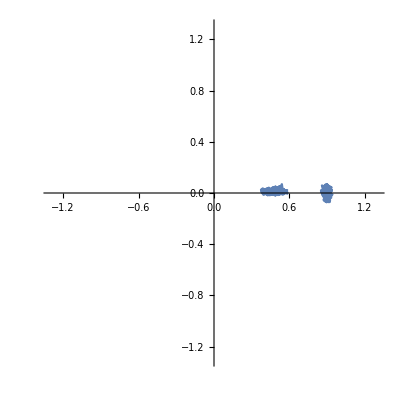

{{A→-0.130137,B→0.557081,TR→55440.9},{A→-0.138163,B→0.563835,TR→45788.8},{A→-0.139515,B→0.583359,TR→46935.},{A→-0.128951,B→0.554821,TR→50403.4},{A→-0.130273,B→0.592131,TR→62537.5},{A→-0.1396,B→0.588565,TR→53250.4},{A→-0.133808,B→0.575077,TR→48798.1},{A→-0.129729,B→0.565787,TR→55830.5},{A→-0.134526,B→0.600587,TR→51459.5},{A→-0.155183,B→0.612276,TR→71021.4},{A→-0.135772,B→0.59742,TR→40550.4},{A→-0.158308,B→0.602453,TR→42378.1},{A→-0.147019,B→0.596373,TR→54364.2},{A→-0.13426,B→0.592564,TR→39417.5},{A→-0.133838,B→0.655168,TR→52763.8},{A→-0.131649,B→0.609677,TR→37828.4},{A→-0.122212,B→0.625165,TR→39654.1},{A→-0.134364,B→0.639441,TR→59395.},{A→-0.13265,B→0.602574,TR→52498.4},{A→-0.130243,B→0.606803,TR→52366.8}}

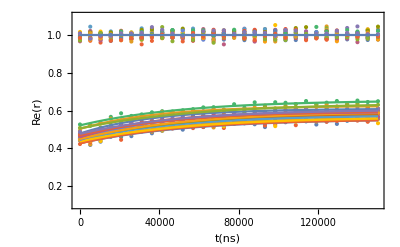

```mathematica
file="E:\\Data\\fluxonium waveguide\\080618_rabi_CH2(AWG1Vpp)_no pump_readout_6.5371GHz__-15dBm_qubit6.4871GHz_-27.5dBm_-0.6_mA_I cos Q sin mod true interleafing_odd readout even ref_avg75k_Rabi150000_duty200000readout5us_loop20.h5";
header=Import[file]
Clear[TR,A,B];
edelay1 = 322;
edelay2 = 322;
Freadout1=6.4871;
Freadout2 = 6.5871;
stepFreq=0.0001;
powerReadout=-15;
phaseoffset1=-0.35π/2;
phaseoffset2 = -1.9π / 2;
powerRef=5;
numberloop =20;
numberRabidata =30;
initguessS={{A,0.2},{B,0.4},{TR,20000}};
BoundS={0>A>-1,1>B>0,TR>0};
refPoint1=IntegerPart[1+(Freadout1-6.3)/stepFreq];
refPoint2=IntegerPart[1+(Freadout2-6.3)/stepFreq];
delays = Flatten@Import[file,{"Datasets",3}];
(*ListLinePlot[delays]*)
amp=Flatten@Import[file,{"Datasets",1}];
(*ListLinePlot[amp]*)
tempamp = Table[amp[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempamp = Table[amp[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
phase=Flatten@Import[file,{"Datasets",2}];
(*ListLinePlot[phase]*)
For[i=1,i<numberloop*numberRabidata*2,i++,If[phase[[i]]>0,phase[[i]]=phase[[i]]-2*π,phase[[i]]=phase[[i]]]];
tempphase = Table[phase[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempphase = Table[phase[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
Rabirefl2=10^(-(powerReadout-powerRef)/20)*Rabiamp*Exp[I*(Rabiphase-edelay1*Freadout1+phaseoffset1)]/ampref[[refPoint1]];
Refrefl2 = 10^(-(powerReadout-powerRef)/20)*Refamp*Exp[I*(Refphase-edelay2*Freadout2+phaseoffset2)]/ampref[[refPoint2]];
Show[ListLinePlot[Transpose@{Flatten@Re[Rabirefl2],Flatten@Im[Rabirefl2]},PlotRange->{{-1.3,1.3},{-1.3,1.3}}, AspectRatio->1],ListLinePlot[Transpose@{Flatten@Re[Refrefl2],Flatten@Im[Refrefl2]}]]
avgRef2=Mean[Re[Refrefl2]];
(*p02Rabi=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]},PlotRange->{-0.5,1.3}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]},PlotRange->{0.0,1.3}, PlotStyle->Brown],Plot[avgRef2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
shift2=1-avgRef2;
(*p02Rabishift=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]+shift2},PlotRange->{-0.5,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]+shift2},PlotRange->{-0.3,1.1}, PlotStyle->Brown],Plot[avgRef2+shift2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
scale2=1/avgRef2;
scalefit27p5dB=Table[FindFit[Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}],{A*Exp[-t/TR]+B,BoundS},initguessS,t],{loopi,1,numberloop}]
Rabirefl2table=ArrayReshape[Rabirefl2,{10,30}];
listplottable=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,150000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
listplottable2=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Refrefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,210000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
fit2table=A*Exp[-t/TR]+B/.scalefit27p5dB;
p03drive10usscale100us=Show[listplottable,listplottable2,Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All],Plot[fit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
```

{55440.9,45788.8,46935.,50403.4,62537.5,53250.4,48798.1,55830.5,51459.5,71021.4,40550.4,42378.1,54364.2,39417.5,52763.8,37828.4,39654.1,59395.,52498.4,52366.8}

50634.1

8389.95

-0.13601

0.596058

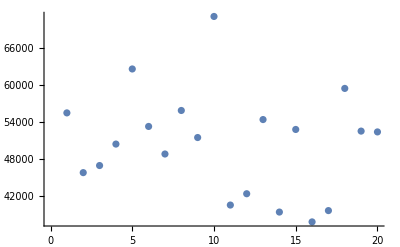

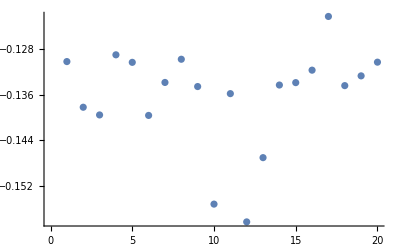

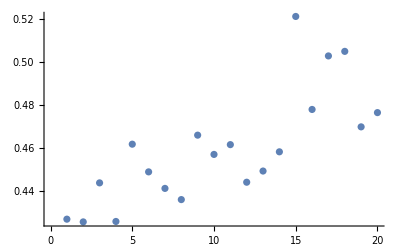

```mathematica
TR/.scalefit27p5dB
Tp27p5=Mean[TR/.scalefit27p5dB]
Std27p5=StandardDeviation[TR/.scalefit27p5dB]
A27p5=Mean[A/.scalefit27p5dB]
B27p5=Mean[B/.scalefit27p5dB]
Averaged27p5=Mean@Table[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2,{loopi,1,numberloop}];
ListPlot[TR/.scalefit27p5dB]
ListPlot[A/.scalefit27p5dB]
ListPlot[B+A/.scalefit27p5dB]
```

#### Transient: AWG Ch2 drive with 0-3, SGMA -25dBm, Ch3 read, power -15 dBm @-0.6mA loop 30

{/demod_Magnitude0,/demod_Phase0,/rabi_table}

{/demod_Magnitude0,/demod_Phase0,/rabi_table}

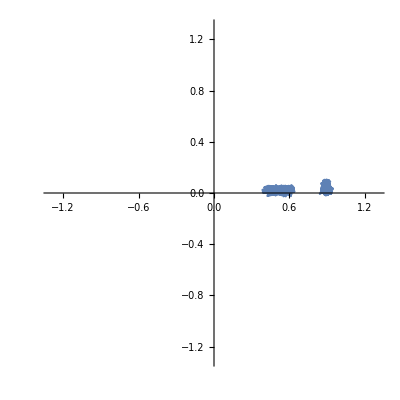

{{A→-0.204716,B→0.6525,TR→45889.2},{A→-0.210392,B→0.675315,TR→52936.2},{A→-0.212075,B→0.698402,TR→55564.2},{A→-0.192442,B→0.674224,TR→61134.6},{A→-0.196606,B→0.674764,TR→41545.8},{A→-0.204675,B→0.658694,TR→30608.3},{A→-0.204078,B→0.683899,TR→42375.},{A→-0.180429,B→0.665995,TR→38829.5},{A→-0.187149,B→0.65662,TR→50586.7},{A→-0.178685,B→0.629687,TR→46908.8},{A→-0.179605,B→0.646501,TR→40653.7},{A→-0.190844,B→0.64788,TR→52038.2},{A→-0.181514,B→0.660232,TR→40562.8},{A→-0.190275,B→0.653048,TR→37510.9},{A→-0.194244,B→0.647023,TR→45919.3},{A→-0.184966,B→0.64061,TR→36252.7},{A→-0.200292,B→0.676191,TR→57424.7},{A→-0.183394,B→0.669374,TR→43914.4},{A→-0.185472,B→0.688468,TR→33173.5},{A→-0.185141,B→0.686265,TR→32879.9},{A→-0.180036,B→0.688816,TR→36318.9},{A→-0.170789,B→0.68225,TR→42182.2},{A→-0.192332,B→0.675867,TR→35011.3},{A→-0.187709,B→0.693926,TR→33223.3},{A→-0.190918,B→0.697485,TR→33290.5},{A→-0.183498,B→0.679218,TR→43250.},{A→-0.173689,B→0.658008,TR→35816.1},{A→-0.188098,B→0.670287,TR→30153.5},{A→-0.18833,B→0.617739,TR→41889.8},{A→-0.190043,B→0.644546,TR→41693.4}}

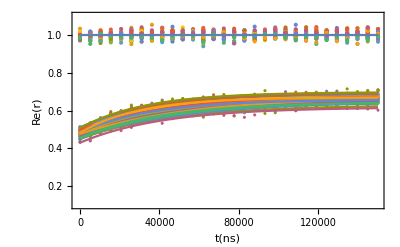

```mathematica
file1="E:\\Data\\fluxonium waveguide\\080618_rabi_CH2(AWG1Vpp)_no pump_readout_6.5371GHz__-15dBm_qubit6.4871GHz_-25dBm_-0.6_mA_I cos Q sin mod true interleafing_odd readout even ref_avg75k_Rabi150000_duty200000readout5us_loop20.h5";
header=Import[file1]
file2="E:\\Data\\fluxonium waveguide\\080618_rabi_CH2(AWG1Vpp)_no pump_readout_6.5371GHz__-15dBm_qubit6.4871GHz_-25dBm_-0.6_mA_I cos Q sin mod true interleafing_odd readout even ref_avg75k_Rabi150000_duty200000readout5us_loop20_2.h5";
header=Import[file2]
Clear[TR,A,B];
edelay1 = 322;
edelay2 = 322;
Freadout1=6.4871;
Freadout2 = 6.5871;
stepFreq=0.0001;
powerReadout=-15;
phaseoffset1=-0.35π/2;
phaseoffset2 = -1.9π / 2;
powerRef=5;
numberloop =30;
numberRabidata =30;
initguessS={{A,0.2},{B,0.4},{TR,20000}};
BoundS={0>A>-1,1>B>0,TR>0};
refPoint1=IntegerPart[1+(Freadout1-6.3)/stepFreq];
refPoint2=IntegerPart[1+(Freadout2-6.3)/stepFreq];
delays = Flatten@Join[Import[file1,{"Datasets",3}],Import[file2,{"Datasets",3}]];
(*ListLinePlot[delays]*)
amp=Flatten@Join[Import[file1,{"Datasets",1}],Import[file2,{"Datasets",1}]];
(*ListLinePlot[amp]*)
tempamp = Table[amp[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempamp = Table[amp[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
phase=Flatten@Join[Import[file1,{"Datasets",2}],Import[file2,{"Datasets",2}]];
(*ListLinePlot[phase]*)
For[i=1,i<numberloop*numberRabidata*2,i++,If[phase[[i]]>0,phase[[i]]=phase[[i]]-2*π,phase[[i]]=phase[[i]]]];
tempphase = Table[phase[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempphase = Table[phase[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
Rabirefl2=10^(-(powerReadout-powerRef)/20)*Rabiamp*Exp[I*(Rabiphase-edelay1*Freadout1+phaseoffset1)]/ampref[[refPoint1]];
Refrefl2 = 10^(-(powerReadout-powerRef)/20)*Refamp*Exp[I*(Refphase-edelay2*Freadout2+phaseoffset2)]/ampref[[refPoint2]];
Show[ListLinePlot[Transpose@{Flatten@Re[Rabirefl2],Flatten@Im[Rabirefl2]},PlotRange->{{-1.3,1.3},{-1.3,1.3}}, AspectRatio->1],ListLinePlot[Transpose@{Flatten@Re[Refrefl2],Flatten@Im[Refrefl2]}]]
avgRef2=Mean[Re[Refrefl2]];
(*p02Rabi=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]},PlotRange->{-0.5,1.3}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]},PlotRange->{0.0,1.3}, PlotStyle->Brown],Plot[avgRef2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
shift2=1-avgRef2;
(*p02Rabishift=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]+shift2},PlotRange->{-0.5,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]+shift2},PlotRange->{-0.3,1.1}, PlotStyle->Brown],Plot[avgRef2+shift2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
scale2=1/avgRef2;
scalefit25dB=Table[FindFit[Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}],{A*Exp[-t/TR]+B,BoundS},initguessS,t],{loopi,1,numberloop}]
Rabirefl2table=ArrayReshape[Rabirefl2,{1,30}];
listplottable=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,150000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
listplottable2=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Refrefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,210000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
fit2table=A*Exp[-t/TR]+B/.scalefit25dB;
p03drive10usscale100us=Show[listplottable,listplottable2,Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All],Plot[fit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
```

{45889.2,52936.2,55564.2,61134.6,41545.8,30608.3,42375.,38829.5,50586.7,46908.8,40653.7,52038.2,40562.8,37510.9,45919.3,36252.7,57424.7,43914.4,33173.5,32879.9,36318.9,42182.2,35011.3,33223.3,33290.5,43250.,35816.1,30153.5,41889.8,41693.4}

41984.6

8121.87

-0.189748

0.666461

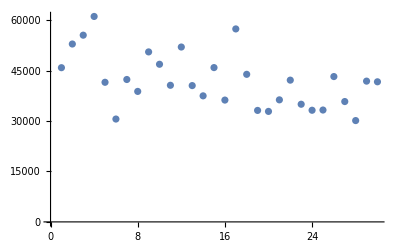

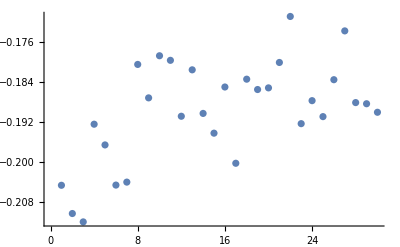

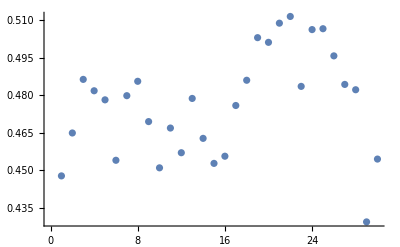

```mathematica
TR/.scalefit25dB
Tp25=Mean[TR/.scalefit25dB]
Std25=StandardDeviation[TR/.scalefit25dB]
A25=Mean[A/.scalefit25dB]
B25=Mean[B/.scalefit25dB]
Averaged25=Mean@Table[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2,{loopi,1,numberloop}];
ListPlot[TR/.scalefit25dB]
ListPlot[A/.scalefit25dB]
ListPlot[B+A/.scalefit25dB]
```

#### Transient: AWG Ch2 drive with 0-3, SGMA -22.5dBm, Ch3 read, power -15 dBm @-0.6mA loop 11

{/demod_Magnitude0,/demod_Phase0,/rabi_table}

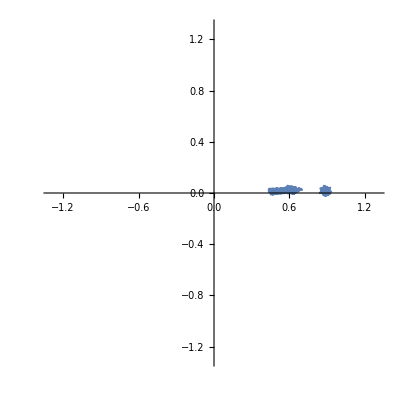

{{A→-0.240843,B→0.73656,TR→26344.1},{A→-0.231583,B→0.771117,TR→33105.8},{A→-0.215519,B→0.736178,TR→37527.6},{A→-0.220705,B→0.727507,TR→27477.9},{A→-0.209671,B→0.697903,TR→37844.8},{A→-0.207689,B→0.715971,TR→37778.},{A→-0.209174,B→0.715453,TR→41318.2},{A→-0.190473,B→0.70544,TR→50540.2},{A→-0.201078,B→0.705089,TR→40843.6},{A→-0.213294,B→0.708711,TR→38836.7},{A→-0.213976,B→0.716757,TR→35040.8}}

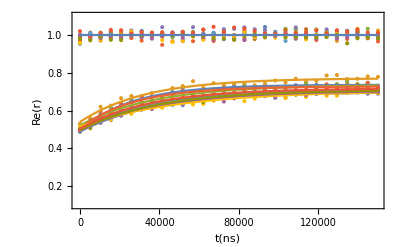

```mathematica
file="E:\\Data\\fluxonium waveguide\\080618_rabi_CH2(AWG1Vpp)_no pump_readout_6.5371GHz__-15dBm_qubit6.4871GHz_-22.5dBm_-0.6_mA_I cos Q sin mod true interleafing_odd readout even ref_avg75k_Rabi150000_duty200000readout5us_loop11.h5";
header=Import[file]
Clear[TR,A,B];
edelay1 = 322;
edelay2 = 322;
Freadout1=6.4871;
Freadout2 = 6.5871;
stepFreq=0.0001;
powerReadout=-15;
phaseoffset1=-0.35π/2;
phaseoffset2 = -1.9π / 2;
powerRef=5;
numberloop =11;
numberRabidata =30;
initguessS={{A,0.2},{B,0.4},{TR,20000}};
BoundS={0>A>-1,1>B>0,TR>0};
refPoint1=IntegerPart[1+(Freadout1-6.3)/stepFreq];
refPoint2=IntegerPart[1+(Freadout2-6.3)/stepFreq];
delays = Flatten@Import[file,{"Datasets",3}];
(*ListLinePlot[delays]*)
amp=Flatten@Import[file,{"Datasets",1}];
(*ListLinePlot[amp]*)
tempamp = Table[amp[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempamp = Table[amp[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
phase=Flatten@Import[file,{"Datasets",2}];
(*ListLinePlot[phase]*)
For[i=1,i<numberloop*numberRabidata*2,i++,If[phase[[i]]>0,phase[[i]]=phase[[i]]-2*π,phase[[i]]=phase[[i]]]];
tempphase = Table[phase[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempphase = Table[phase[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
Rabirefl2=10^(-(powerReadout-powerRef)/20)*Rabiamp*Exp[I*(Rabiphase-edelay1*Freadout1+phaseoffset1)]/ampref[[refPoint1]];
Refrefl2 = 10^(-(powerReadout-powerRef)/20)*Refamp*Exp[I*(Refphase-edelay2*Freadout2+phaseoffset2)]/ampref[[refPoint2]];
Show[ListLinePlot[Transpose@{Flatten@Re[Rabirefl2],Flatten@Im[Rabirefl2]},PlotRange->{{-1.3,1.3},{-1.3,1.3}}, AspectRatio->1],ListLinePlot[Transpose@{Flatten@Re[Refrefl2],Flatten@Im[Refrefl2]}]]
avgRef2=Mean[Re[Refrefl2]];
(*p02Rabi=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]},PlotRange->{-0.5,1.3}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]},PlotRange->{0.0,1.3}, PlotStyle->Brown],Plot[avgRef2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
shift2=1-avgRef2;
(*p02Rabishift=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]+shift2},PlotRange->{-0.5,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]+shift2},PlotRange->{-0.3,1.1}, PlotStyle->Brown],Plot[avgRef2+shift2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
scale2=1/avgRef2;
scalefit22p5dB=Table[FindFit[Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}],{A*Exp[-t/TR]+B,BoundS},initguessS,t],{loopi,1,numberloop}]
Rabirefl2table=ArrayReshape[Rabirefl2,{10,30}];
listplottable=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,150000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
listplottable2=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Refrefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,210000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
fit2table=A*Exp[-t/TR]+B/.scalefit22p5dB;
p03drive10usscale100us=Show[listplottable,listplottable2,Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All],Plot[fit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
```

{26344.1,33105.8,37527.6,27477.9,37844.8,37778.,41318.2,50540.2,40843.6,38836.7,35040.8}

36968.9

6670.36

-0.214

0.721517

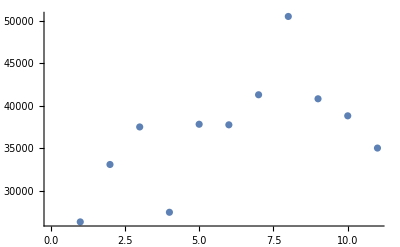

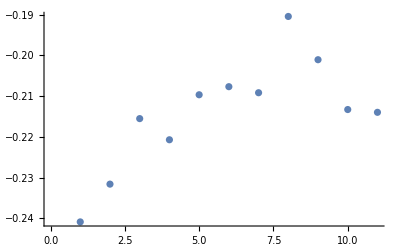

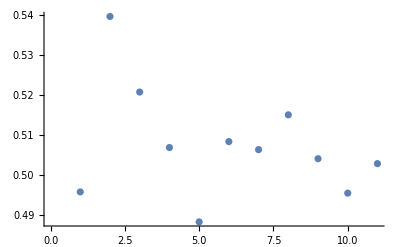

```mathematica
TR/.scalefit22p5dB
Tp22p5=Mean[TR/.scalefit22p5dB]
Std22p5=StandardDeviation[TR/.scalefit22p5dB]
A22p5=Mean[A/.scalefit22p5dB]
B22p5=Mean[B/.scalefit22p5dB]
Averaged22p5=Mean@Table[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2,{loopi,1,numberloop}];
ListPlot[TR/.scalefit22p5dB]
ListPlot[A/.scalefit22p5dB]
ListPlot[B+A/.scalefit22p5dB]
```

#### Transient: AWG Ch2 drive with 0-3, SGMA -20dBm, Ch3 read, power -15 dBm @-0.6mA loop 20

{/demod_Magnitude0,/demod_Phase0,/rabi_table}

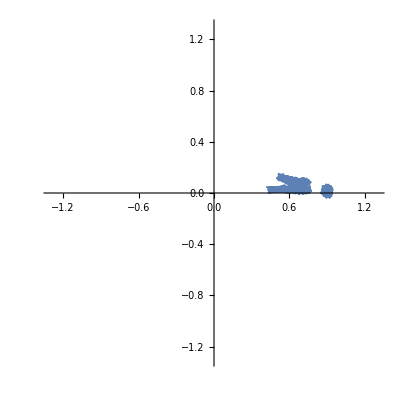

{{A→-0.264389,B→0.757038,TR→23492.},{A→-0.262632,B→0.766301,TR→25245.6},{A→-0.247471,B→0.789249,TR→34092.8},{A→-0.237975,B→0.791416,TR→28762.4},{A→-0.253761,B→0.806875,TR→24740.9},{A→-0.270249,B→0.804305,TR→22232.8},{A→-0.246749,B→0.830076,TR→15165.},{A→-0.246183,B→0.820458,TR→17367.7},{A→-0.251618,B→0.825219,TR→14560.1},{A→-0.247323,B→0.795336,TR→20018.3},{A→-0.272676,B→0.789925,TR→20130.6},{A→-0.265608,B→0.79959,TR→22153.9},{A→-0.272283,B→0.812879,TR→19481.1},{A→-0.262703,B→0.83271,TR→21199.7},{A→-0.271507,B→0.786623,TR→22109.8},{A→-0.272796,B→0.786938,TR→18426.9},{A→-0.292588,B→0.772329,TR→17268.},{A→-0.280473,B→0.785667,TR→24036.5},{A→-0.283881,B→0.763251,TR→18918.3},{A→-0.271739,B→0.754763,TR→21519.6},{A→-0.205711,B→0.8207,TR→30842.7},{A→-0.195661,B→0.808477,TR→37909.4},{A→-0.192512,B→0.80591,TR→33894.4},{A→-0.184831,B→0.831801,TR→38593.4},{A→-0.219868,B→0.803108,TR→49383.},{A→-0.214918,B→0.801571,TR→52985.6},{A→-0.183204,B→0.781196,TR→37060.1},{A→-0.193873,B→0.826295,TR→36587.2},{A→-0.193411,B→0.812345,TR→34204.7},{A→-0.184537,B→0.824204,TR→43164.5},{A→-0.214498,B→0.812015,TR→39308.9},{A→-0.196436,B→0.831533,TR→48400.8},{A→-0.223874,B→0.78319,TR→37408.3},{A→-0.202836,B→0.78639,TR→48035.4},{A→-0.224683,B→0.800196,TR→34997.9},{A→-0.214838,B→0.784199,TR→38663.2},{A→-0.225268,B→0.779997,TR→42337.9},{A→-0.216292,B→0.805033,TR→39892.2}}

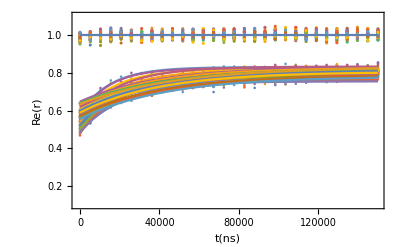

```mathematica
file1="E:\\Data\\fluxonium waveguide\\080418_rabi_CH2(AWG1Vpp)_no pump_readout_6.5371GHz__-15dBm_qubit6.4871GHz_-20dBm_-0.6_mA_I cos Q sin mod true interleafing_odd readout even ref_avg75k_Rabi150000_duty200000readout5us_loop20.h5";
header=Import[file1]
file2="E:\\Data\\fluxonium waveguide\\080718_rabi_CH2(AWG1Vpp)_no pump_readout_6.5371GHz__-15dBm_qubit6.4871GHz_-20dBm_-0.6_mA_I cos Q sin mod true interleafing_odd readout even ref_avg75k_Rabi150000_duty200000readout5us_loop18.h5";
Clear[TR,A,B];
edelay1 = 322;
edelay2 = 322;
Freadout1=6.4871;
Freadout2 = 6.5871;
stepFreq=0.0001;
powerReadout=-15;
phaseoffset1=-0.35π/2;
phaseoffset2 = -1.9π / 2;
powerRef=5;
numberloop =38;
numberRabidata =30;
initguessS={{A,0.2},{B,0.4},{TR,20000}};
BoundS={0>A>-1,1>B>0,TR>0};
refPoint1=IntegerPart[1+(Freadout1-6.3)/stepFreq];
refPoint2=IntegerPart[1+(Freadout2-6.3)/stepFreq];
delays = Flatten@Join[Import[file1,{"Datasets",3}],Import[file2,{"Datasets",3}]];
(*ListLinePlot[delays]*)
amp=Flatten@Join[Import[file1,{"Datasets",1}],Import[file2,{"Datasets",1}]];
(*ListLinePlot[amp]*)
tempamp = Table[amp[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempamp = Table[amp[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
phase=Flatten@Join[Import[file1,{"Datasets",2}],Import[file2,{"Datasets",2}]];
(*ListLinePlot[phase]*)
For[i=1,i<numberloop*numberRabidata*2,i++,If[phase[[i]]>0,phase[[i]]=phase[[i]]-2*π,phase[[i]]=phase[[i]]]];
tempphase = Table[phase[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempphase = Table[phase[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
Rabirefl2=10^(-(powerReadout-powerRef)/20)*Rabiamp*Exp[I*(Rabiphase-edelay1*Freadout1+phaseoffset1)]/ampref[[refPoint1]];
Refrefl2 = 10^(-(powerReadout-powerRef)/20)*Refamp*Exp[I*(Refphase-edelay2*Freadout2+phaseoffset2)]/ampref[[refPoint2]];
Show[ListLinePlot[Transpose@{Flatten@Re[Rabirefl2],Flatten@Im[Rabirefl2]},PlotRange->{{-1.3,1.3},{-1.3,1.3}}, AspectRatio->1],ListLinePlot[Transpose@{Flatten@Re[Refrefl2],Flatten@Im[Refrefl2]}]]
avgRef2=Mean[Re[Refrefl2]];
(*p02Rabi=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]},PlotRange->{-0.5,1.3}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]},PlotRange->{0.0,1.3}, PlotStyle->Brown],Plot[avgRef2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
shift2=1-avgRef2;
(*p02Rabishift=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]+shift2},PlotRange->{-0.5,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]+shift2},PlotRange->{-0.3,1.1}, PlotStyle->Brown],Plot[avgRef2+shift2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
scale2=1/avgRef2;
scalefit20dB=Table[FindFit[Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}],{A*Exp[-t/TR]+B,BoundS},initguessS,t],{loopi,1,numberloop}]
Rabirefl2table=ArrayReshape[Rabirefl2,{10,30}];
listplottable=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,150000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
listplottable2=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Refrefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,210000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
fit2table=A*Exp[-t/TR]+B/.scalefit20dB;
p03drive10usscale100us=Show[listplottable,listplottable2,Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All],Plot[fit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
```

{23492.,25245.6,34092.8,28762.4,24740.9,22232.8,15165.,17367.7,14560.1,20018.3,20130.6,22153.9,19481.1,21199.7,22109.8,18426.9,17268.,24036.5,18918.3,21519.6,30842.7,37909.4,33894.4,38593.4,49383.,52985.6,37060.1,36587.2,34204.7,43164.5,39308.9,48400.8,37408.3,48035.4,34997.9,38663.2,42337.9,39892.2}

30384.

10799.1

-0.235838

0.799187

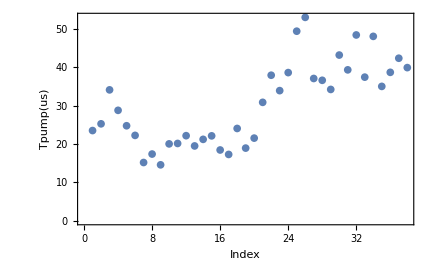

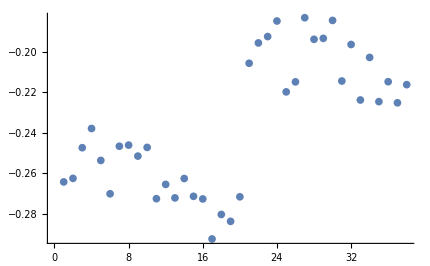

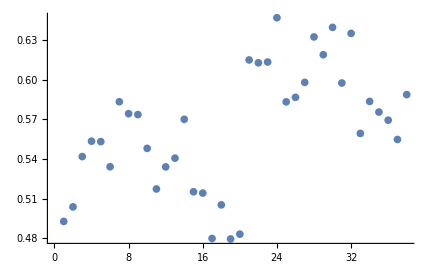

```mathematica
TR/.scalefit20dB
Tp20=Mean[TR/.scalefit20dB]
Std20=StandardDeviation[TR/.scalefit20dB]
A20=Mean[A/.scalefit20dB]
B20=Mean[B/.scalefit20dB]
Averaged20=Mean@Table[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2,{loopi,1,numberloop}];
ListPlot[TR/1000/.scalefit20dB, LabelStyle->Large, Frame->True,FrameLabel->{"Index","Tpump(us)"}]
ListPlot[A/.scalefit20dB]
ListPlot[B+A/.scalefit20dB]
```

#### Transient: AWG Ch2 drive with 0-3, SGMA -17.5dBm, Ch3 read, power -15 dBm @-0.6mA loop 20

{/demod_Magnitude0,/demod_Phase0,/rabi_table}

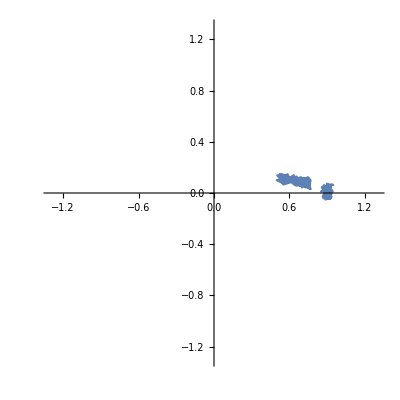

{{A→-0.255592,B→0.837286,TR→41948.1},{A→-0.271721,B→0.839233,TR→34928.1},{A→-0.258351,B→0.835373,TR→40579.1},{A→-0.247709,B→0.816769,TR→29657.4},{A→-0.234867,B→0.833786,TR→24640.5},{A→-0.251976,B→0.837727,TR→26368.5}}

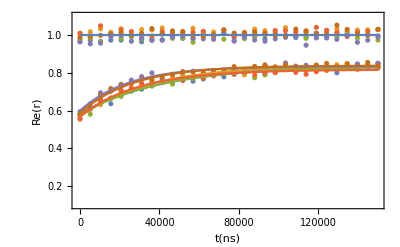

```mathematica
file="E:\\Data\\fluxonium waveguide\\080718_rabi_CH2(AWG1Vpp)_no pump_readout_6.5371GHz__-15dBm_qubit6.4871GHz_-17.5dBm_-0.6_mA_I cos Q sin mod true interleafing_odd readout even ref_avg75k_Rabi150000_duty200000readout5us_loop6.h5";
header=Import[file]
Clear[TR,A,B];
edelay1 = 322;
edelay2 = 322;
Freadout1=6.4871;
Freadout2 = 6.5871;
stepFreq=0.0001;
powerReadout=-15;
phaseoffset1=-0.35π/2;
phaseoffset2 = -1.9π / 2;
powerRef=5;
numberloop =6;
numberRabidata =30;
initguessS={{A,0.2},{B,0.4},{TR,20000}};
BoundS={0>A>-1,1>B>0,TR>0};
refPoint1=IntegerPart[1+(Freadout1-6.3)/stepFreq];
refPoint2=IntegerPart[1+(Freadout2-6.3)/stepFreq];
delays = Flatten@Import[file,{"Datasets",3}];
(*ListLinePlot[delays]*)
amp=Flatten@Import[file,{"Datasets",1}];
(*ListLinePlot[amp]*)
tempamp = Table[amp[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempamp = Table[amp[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
phase=Flatten@Import[file,{"Datasets",2}];
(*ListLinePlot[phase]*)
For[i=1,i<numberloop*numberRabidata*2,i++,If[phase[[i]]>0,phase[[i]]=phase[[i]]-2*π,phase[[i]]=phase[[i]]]];
tempphase = Table[phase[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempphase = Table[phase[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
Rabirefl2=10^(-(powerReadout-powerRef)/20)*Rabiamp*Exp[I*(Rabiphase-edelay1*Freadout1+phaseoffset1)]/ampref[[refPoint1]];
Refrefl2 = 10^(-(powerReadout-powerRef)/20)*Refamp*Exp[I*(Refphase-edelay2*Freadout2+phaseoffset2)]/ampref[[refPoint2]];
Show[ListLinePlot[Transpose@{Flatten@Re[Rabirefl2],Flatten@Im[Rabirefl2]},PlotRange->{{-1.3,1.3},{-1.3,1.3}}, AspectRatio->1],ListLinePlot[Transpose@{Flatten@Re[Refrefl2],Flatten@Im[Refrefl2]}]]
avgRef2=Mean[Re[Refrefl2]];
(*p02Rabi=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]},PlotRange->{-0.5,1.3}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]},PlotRange->{0.0,1.3}, PlotStyle->Brown],Plot[avgRef2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
shift2=1-avgRef2;
(*p02Rabishift=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]+shift2},PlotRange->{-0.5,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]+shift2},PlotRange->{-0.3,1.1}, PlotStyle->Brown],Plot[avgRef2+shift2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
scale2=1/avgRef2;
scalefit17p5dB=Table[FindFit[Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}],{A*Exp[-t/TR]+B,BoundS},initguessS,t],{loopi,1,numberloop}]
Rabirefl2table=ArrayReshape[Rabirefl2,{10,30}];
listplottable=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,150000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
listplottable2=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Refrefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,210000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
fit2table=A*Exp[-t/TR]+B/.scalefit17p5dB;
p03drive10usscale100us=Show[listplottable,listplottable2,Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All],Plot[fit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
```

{41948.1,34928.1,40579.1,29657.4,24640.5,26368.5}

26888.8

2548.6

-0.244851

0.833362

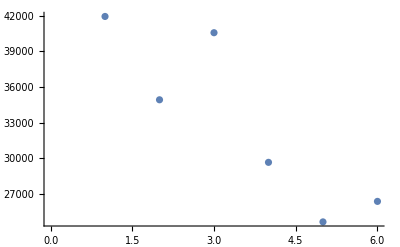

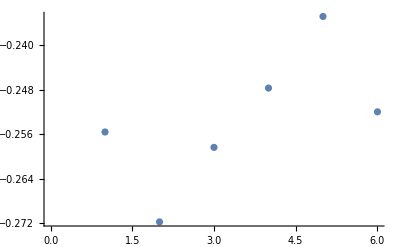

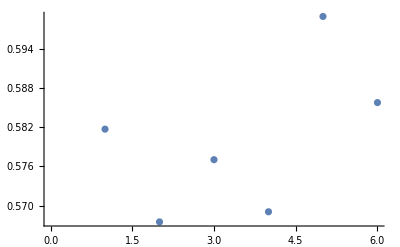

```mathematica
TR/.scalefit17p5dB
Tp17p5=Mean[Drop[TR/.scalefit17p5dB,3]]
Std17p5=StandardDeviation[Drop[TR/.scalefit17p5dB,3]]
A17p5=Mean[Drop[A/.scalefit17p5dB,3]]
B17p5=Mean[B/.scalefit17p5dB]
Averaged17p5=Mean@Table[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2,{loopi,1,numberloop}];
ListPlot[TR/.scalefit17p5dB]
ListPlot[A/.scalefit17p5dB]
ListPlot[B+A/.scalefit17p5dB]
```

#### Transient: AWG Ch2 drive with 0-3, SGMA -15dBm, Ch3 read, power -15 dBm @-0.6mA loop 20

{/demod_Magnitude0,/demod_Phase0,/rabi_table}

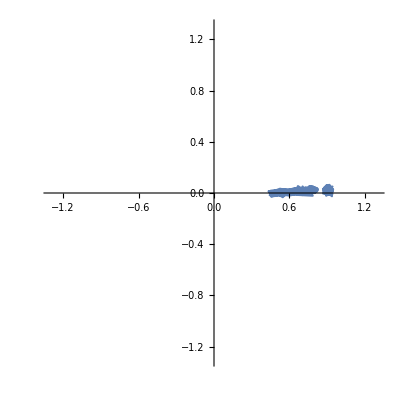

{{A→-0.343468,B→0.851238,TR→11808.4},{A→-0.327576,B→0.881765,TR→12032.6},{A→-0.34736,B→0.87851,TR→10495.4},{A→-0.310517,B→0.867541,TR→19860.7},{A→-0.32187,B→0.858834,TR→21594.4},{A→-0.340567,B→0.85046,TR→22042.6},{A→-0.321313,B→0.870025,TR→22514.4},{A→-0.305728,B→0.856363,TR→23310.2},{A→-0.323711,B→0.841253,TR→21682.6},{A→-0.323731,B→0.846416,TR→19521.3},{A→-0.332991,B→0.830436,TR→13902.},{A→-0.346873,B→0.851793,TR→13560.2},{A→-0.357029,B→0.85915,TR→15839.4},{A→-0.326673,B→0.866153,TR→18792.4},{A→-0.328193,B→0.838874,TR→17969.1},{A→-0.303532,B→0.851445,TR→20179.7},{A→-0.308276,B→0.837867,TR→25493.7},{A→-0.286511,B→0.844749,TR→25772.7},{A→-0.296125,B→0.860232,TR→22750.8},{A→-0.285649,B→0.838504,TR→29816.}}

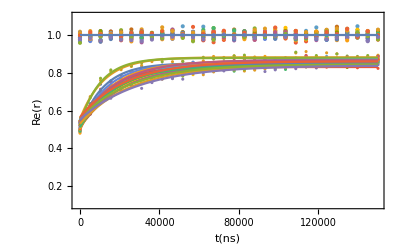

```mathematica
file="E:\\Data\\fluxonium waveguide\\080418_rabi_CH2(AWG1Vpp)_no pump_readout_6.5371GHz__-15dBm_qubit6.4871GHz_-15dBm_-0.6_mA_I cos Q sin mod true interleafing_odd readout even ref_avg75k_Rabi150000_duty200000readout5us_loop20.h5";
header=Import[file]
Clear[TR,A,B];
edelay1 = 322;
edelay2 = 322;
Freadout1=6.4871;
Freadout2 = 6.5871;
stepFreq=0.0001;
powerReadout=-15;
phaseoffset1=-0.35π/2;
phaseoffset2 = -1.9π / 2;
powerRef=5;
numberloop =20;
numberRabidata =30;
initguessS={{A,0.2},{B,0.4},{TR,20000}};
BoundS={0>A>-1,1>B>0,TR>0};
refPoint1=IntegerPart[1+(Freadout1-6.3)/stepFreq];
refPoint2=IntegerPart[1+(Freadout2-6.3)/stepFreq];
delays = Flatten@Import[file,{"Datasets",3}];
(*ListLinePlot[delays]*)
amp=Flatten@Import[file,{"Datasets",1}];
(*ListLinePlot[amp]*)
tempamp = Table[amp[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempamp = Table[amp[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
phase=Flatten@Import[file,{"Datasets",2}];
(*ListLinePlot[phase]*)
For[i=1,i<numberloop*numberRabidata*2,i++,If[phase[[i]]>0,phase[[i]]=phase[[i]]-2*π,phase[[i]]=phase[[i]]]];
tempphase = Table[phase[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempphase = Table[phase[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
Rabirefl2=10^(-(powerReadout-powerRef)/20)*Rabiamp*Exp[I*(Rabiphase-edelay1*Freadout1+phaseoffset1)]/ampref[[refPoint1]];
Refrefl2 = 10^(-(powerReadout-powerRef)/20)*Refamp*Exp[I*(Refphase-edelay2*Freadout2+phaseoffset2)]/ampref[[refPoint2]];
Show[ListLinePlot[Transpose@{Flatten@Re[Rabirefl2],Flatten@Im[Rabirefl2]},PlotRange->{{-1.3,1.3},{-1.3,1.3}}, AspectRatio->1],ListLinePlot[Transpose@{Flatten@Re[Refrefl2],Flatten@Im[Refrefl2]}]]
avgRef2=Mean[Re[Refrefl2]];
(*p02Rabi=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]},PlotRange->{-0.5,1.3}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]},PlotRange->{0.0,1.3}, PlotStyle->Brown],Plot[avgRef2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
shift2=1-avgRef2;
(*p02Rabishift=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]+shift2},PlotRange->{-0.5,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]+shift2},PlotRange->{-0.3,1.1}, PlotStyle->Brown],Plot[avgRef2+shift2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
scale2=1/avgRef2;
scalefit15dB=Table[FindFit[Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}],{A*Exp[-t/TR]+B,BoundS},initguessS,t],{loopi,1,numberloop}]
Rabirefl2table=ArrayReshape[Rabirefl2,{10,30}];
listplottable=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,150000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
listplottable2=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Refrefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,210000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
fit2table=A*Exp[-t/TR]+B/.scalefit15dB;
p03drive10usscale100us=Show[listplottable,listplottable2,Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All],Plot[fit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
```

{11808.4,12032.6,10495.4,19860.7,21594.4,22042.6,22514.4,23310.2,21682.6,19521.3,13902.,13560.2,15839.4,18792.4,17969.1,20179.7,25493.7,25772.7,22750.8,29816.}

19446.9

5185.43

-0.321885

0.85408

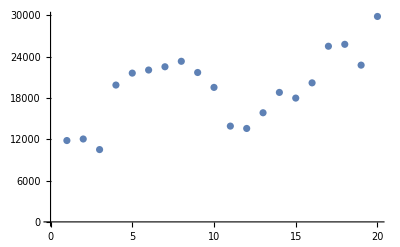

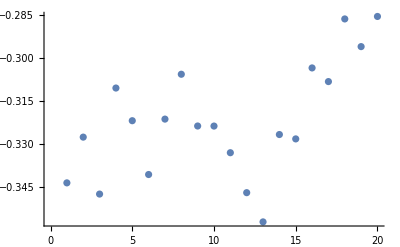

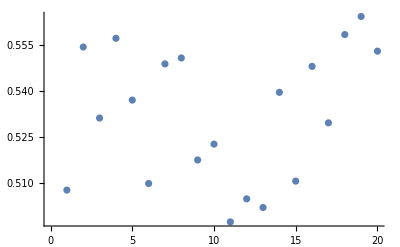

```mathematica
TR/.scalefit15dB
Tp15=Mean[TR/.scalefit15dB]
Std15=StandardDeviation[TR/.scalefit15dB]
A15=Mean[A/.scalefit15dB]
B15=Mean[B/.scalefit15dB]
Averaged15=Mean@Table[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2,{loopi,1,numberloop}];
ListPlot[TR/.scalefit15dB]
ListPlot[A/.scalefit15dB]
ListPlot[B+A/.scalefit15dB]
```

#### Transient: AWG Ch2 drive with 0-3, SGMA -10dBm, Ch3 read, power -15 dBm @-0.6mA loop 20

{/demod_Magnitude0,/demod_Phase0,/rabi_table}

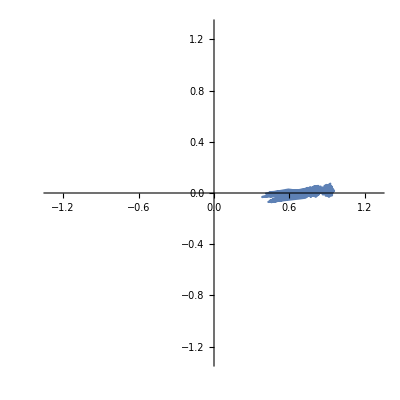

{{A→-0.317503,B→0.868013,TR→15684.4},{A→-0.272457,B→0.867429,TR→22854.4},{A→-0.281263,B→0.855837,TR→22285.5},{A→-0.388851,B→0.880512,TR→6846.67},{A→-0.300621,B→0.902476,TR→16973.5},{A→-0.357171,B→0.887248,TR→10580.3},{A→-0.348678,B→0.881161,TR→7958.56},{A→-0.361677,B→0.866499,TR→6696.39},{A→-0.379807,B→0.898811,TR→6533.25},{A→-0.370755,B→0.896117,TR→6217.89},{A→-0.341286,B→0.915319,TR→6290.24},{A→-0.340118,B→0.877735,TR→784.711},{A→-0.363491,B→0.897682,TR→6288.67},{A→-0.420523,B→0.898101,TR→12693.9},{A→-0.433734,B→0.884747,TR→12410.9},{A→-0.391313,B→0.893588,TR→21051.},{A→-0.383931,B→0.91852,TR→21512.3},{A→-0.397506,B→0.917507,TR→18645.1},{A→-0.412633,B→0.890699,TR→16860.2},{A→-0.38074,B→0.921215,TR→21709.8}}

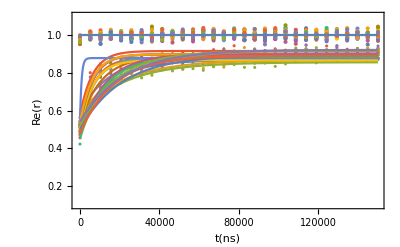

```mathematica
file="E:\\Data\\fluxonium waveguide\\080418_rabi_CH2(AWG1Vpp)_no pump_readout_6.5371GHz__-15dBm_qubit6.4871GHz_-10dBm_-0.6_mA_I cos Q sin mod true interleafing_odd readout even ref_avg75k_Rabi150000_duty200000readout5us_loop20.h5";
header=Import[file]
Clear[TR,A,B];
edelay1 = 322;
edelay2 = 322;
Freadout1=6.4871;
Freadout2 = 6.5871;
stepFreq=0.0001;
powerReadout=-15;
phaseoffset1=-0.35π/2;
phaseoffset2 = -1.9π / 2;
powerRef=5;
numberloop =20;
numberRabidata =30;
initguessS={{A,0.2},{B,0.4},{TR,20000}};
BoundS={0>A>-1,1>B>0,TR>0};
refPoint1=IntegerPart[1+(Freadout1-6.3)/stepFreq];
refPoint2=IntegerPart[1+(Freadout2-6.3)/stepFreq];
delays = Flatten@Import[file,{"Datasets",3}];
(*ListLinePlot[delays]*)
amp=Flatten@Import[file,{"Datasets",1}];
(*ListLinePlot[amp]*)
tempamp = Table[amp[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempamp = Table[amp[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
phase=Flatten@Import[file,{"Datasets",2}];
(*ListLinePlot[phase]*)
For[i=1,i<numberloop*numberRabidata*2,i++,If[phase[[i]]>0,phase[[i]]=phase[[i]]-2*π,phase[[i]]=phase[[i]]]];
tempphase = Table[phase[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempphase = Table[phase[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
Rabirefl2=10^(-(powerReadout-powerRef)/20)*Rabiamp*Exp[I*(Rabiphase-edelay1*Freadout1+phaseoffset1)]/ampref[[refPoint1]];
Refrefl2 = 10^(-(powerReadout-powerRef)/20)*Refamp*Exp[I*(Refphase-edelay2*Freadout2+phaseoffset2)]/ampref[[refPoint2]];
Show[ListLinePlot[Transpose@{Flatten@Re[Rabirefl2],Flatten@Im[Rabirefl2]},PlotRange->{{-1.3,1.3},{-1.3,1.3}}, AspectRatio->1],ListLinePlot[Transpose@{Flatten@Re[Refrefl2],Flatten@Im[Refrefl2]}]]
avgRef2=Mean[Re[Refrefl2]];
(*p02Rabi=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]},PlotRange->{-0.5,1.3}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]},PlotRange->{0.0,1.3}, PlotStyle->Brown],Plot[avgRef2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
shift2=1-avgRef2;
(*p02Rabishift=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]+shift2},PlotRange->{-0.5,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]+shift2},PlotRange->{-0.3,1.1}, PlotStyle->Brown],Plot[avgRef2+shift2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
scale2=1/avgRef2;
scalefit10dB=Table[FindFit[Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}],{A*Exp[-t/TR]+B,BoundS},initguessS,t],{loopi,1,numberloop}]
Rabirefl2table=ArrayReshape[Rabirefl2,{10,30}];
listplottable=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,150000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
listplottable2=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Refrefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,210000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
fit2table=A*Exp[-t/TR]+B/.scalefit10dB;
p03drive10usscale100us=Show[listplottable,listplottable2,Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All],Plot[fit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
```

{15684.4,22854.4,22285.5,6846.67,16973.5,10580.3,7958.56,6696.39,6533.25,6217.89,6290.24,784.711,6288.67,12693.9,12410.9,21051.,21512.3,18645.1,16860.2,21709.8}

13043.9

6892.38

-0.362203

0.890961

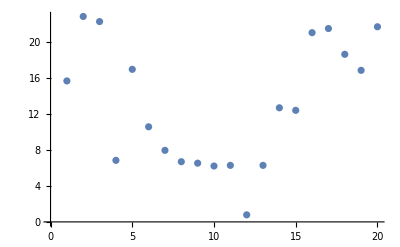

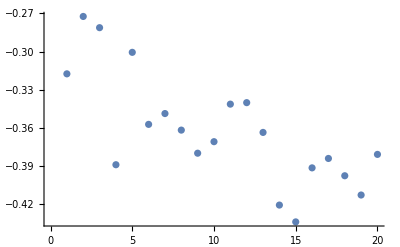

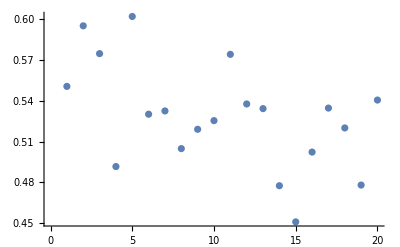

```mathematica
TR/.scalefit10dB
Tp10=Mean[TR/.scalefit10dB]
Std10=StandardDeviation[TR/.scalefit10dB]
A10=Mean[A/.scalefit10dB]
B10=Mean[B/.scalefit10dB]
Averaged10=Mean@Table[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2,{loopi,1,numberloop}];
ListPlot[TR/1000/.scalefit10dB]
ListPlot[A/.scalefit10dB]
ListPlot[B+A/.scalefit10dB]
```

#### Transient: AWG Ch2 drive with 0-3, SGMA -5dBm, Ch3 read, power -15 dBm @-0.6mA loop 20

{/demod_Magnitude0,/demod_Phase0,/rabi_table}

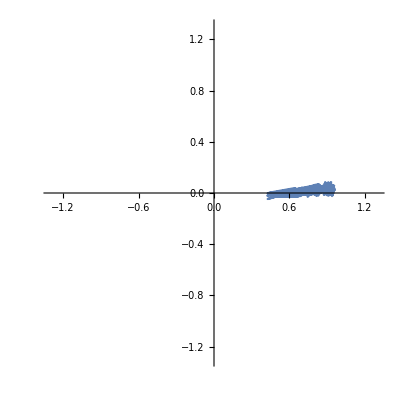

{{A→-0.403879,B→0.923734,TR→17957.9},{A→-0.371369,B→0.908098,TR→14656.9},{A→-0.371839,B→0.928385,TR→13990.4},{A→-0.357377,B→0.906702,TR→14417.2},{A→-0.355564,B→0.867006,TR→13537.5},{A→-0.367114,B→0.867728,TR→13543.8},{A→-0.341817,B→0.922246,TR→14497.1},{A→-0.353813,B→0.872433,TR→12209.8},{A→-0.368093,B→0.917579,TR→11918.6},{A→-0.35638,B→0.892618,TR→12792.9},{A→-0.347106,B→0.871941,TR→14861.3},{A→-0.355595,B→0.869025,TR→13699.5},{A→-0.355317,B→0.893937,TR→15565.4},{A→-0.364582,B→0.874526,TR→15359.7},{A→-0.381715,B→0.907919,TR→15250.5},{A→-0.362175,B→0.861032,TR→12784.6},{A→-0.349568,B→0.897812,TR→12317.3},{A→-0.360918,B→0.89956,TR→13466.8},{A→-0.355345,B→0.916649,TR→12059.8},{A→-0.366411,B→0.925502,TR→12596.9}}

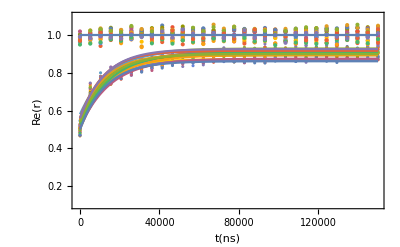

```mathematica
file="E:\\Data\\fluxonium waveguide\\080518_rabi_CH2(AWG1Vpp)_no pump_readout_6.5371GHz__-15dBm_qubit6.4871GHz_-5dBm_-0.6_mA_I cos Q sin mod true interleafing_odd readout even ref_avg75k_Rabi150000_duty200000readout5us_loop20.h5";
header=Import[file]
Clear[TR,A,B];
edelay1 = 322;
edelay2 = 322;
Freadout1=6.4871;
Freadout2 = 6.5871;
stepFreq=0.0001;
powerReadout=-15;
phaseoffset1=-0.35π/2;
phaseoffset2 = -1.9π / 2;
powerRef=5;
numberloop =20;
numberRabidata =30;
initguessS={{A,0.2},{B,0.4},{TR,20000}};
BoundS={0>A>-1,1>B>0,TR>0};
refPoint1=IntegerPart[1+(Freadout1-6.3)/stepFreq];
refPoint2=IntegerPart[1+(Freadout2-6.3)/stepFreq];
delays = Flatten@Import[file,{"Datasets",3}];
(*ListLinePlot[delays]*)
amp=Flatten@Import[file,{"Datasets",1}];
(*ListLinePlot[amp]*)
tempamp = Table[amp[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempamp = Table[amp[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
phase=Flatten@Import[file,{"Datasets",2}];
(*ListLinePlot[phase]*)
For[i=1,i<numberloop*numberRabidata*2,i++,If[phase[[i]]>0,phase[[i]]=phase[[i]]-2*π,phase[[i]]=phase[[i]]]];
tempphase = Table[phase[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempphase = Table[phase[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
Rabirefl2=10^(-(powerReadout-powerRef)/20)*Rabiamp*Exp[I*(Rabiphase-edelay1*Freadout1+phaseoffset1)]/ampref[[refPoint1]];
Refrefl2 = 10^(-(powerReadout-powerRef)/20)*Refamp*Exp[I*(Refphase-edelay2*Freadout2+phaseoffset2)]/ampref[[refPoint2]];
Show[ListLinePlot[Transpose@{Flatten@Re[Rabirefl2],Flatten@Im[Rabirefl2]},PlotRange->{{-1.3,1.3},{-1.3,1.3}}, AspectRatio->1],ListLinePlot[Transpose@{Flatten@Re[Refrefl2],Flatten@Im[Refrefl2]}]]
avgRef2=Mean[Re[Refrefl2]];
(*p02Rabi=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]},PlotRange->{-0.5,1.3}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]},PlotRange->{0.0,1.3}, PlotStyle->Brown],Plot[avgRef2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
shift2=1-avgRef2;
(*p02Rabishift=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]+shift2},PlotRange->{-0.5,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]+shift2},PlotRange->{-0.3,1.1}, PlotStyle->Brown],Plot[avgRef2+shift2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
scale2=1/avgRef2;
scalefit5dB=Table[FindFit[Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}],{A*Exp[-t/TR]+B,BoundS},initguessS,t],{loopi,1,numberloop}]
Rabirefl2table=ArrayReshape[Rabirefl2,{10,30}];
listplottable=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,150000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
listplottable2=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Refrefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,210000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
fit2table=A*Exp[-t/TR]+B/.scalefit5dB;
p03drive10usscale100us=Show[listplottable,listplottable2,Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All],Plot[fit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
```

{17957.9,14656.9,13990.4,14417.2,13537.5,13543.8,14497.1,12209.8,11918.6,12792.9,14861.3,13699.5,15565.4,15359.7,15250.5,12784.6,12317.3,13466.8,12059.8,12596.9}

13874.2

1498.05

-0.362299

0.896222

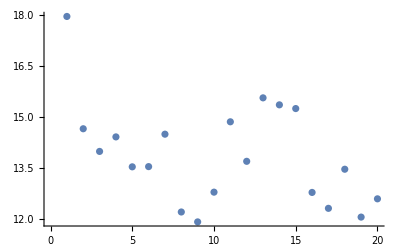

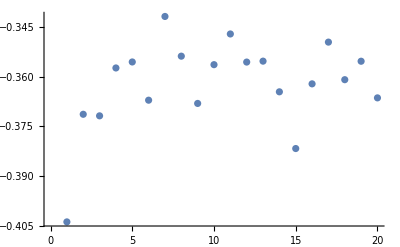

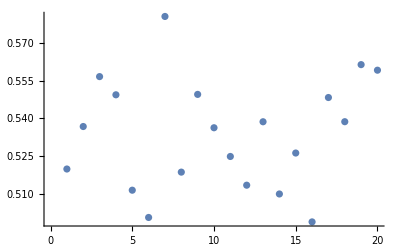

```mathematica
TR/.scalefit5dB
Tp5=Mean[TR/.scalefit5dB]
Std5=StandardDeviation[TR/.scalefit5dB]
A5=Mean[A/.scalefit5dB]
B5=Mean[B/.scalefit5dB]
Averaged5=Mean@Table[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2,{loopi,1,numberloop}];
ListPlot[TR/1000/.scalefit5dB]
ListPlot[A/.scalefit5dB]
ListPlot[B+A/.scalefit5dB]
```

#### Combine

```mathematica
power={-27.5,-25,-22.5,-20,-17.5,-15,-10,-5}
Bs={B27p5,B25,B22p5,B20,B17p5,B15,B10,B5}
Amp={A27p5,A25,A22p5,A20,A17p5,A15,A10,A5}
Tpump={Tp27p5,Tp25,Tp22p5,Tp20,Tp17p5,Tp15,Tp10,Tp5}
σTpump={Std27p5,Std25,Std22p5,Std20,Std17p5,Std15,Std10,Std5}
a=0.000419;
a=0.000419;
G20=0.0026781;
Omega=Sqrt[a*10^((power-5)/10)]
```

{-27.5,-25,-22.5,-20,-17.5,-15,-10,-5}

{0.596058,0.666461,0.721517,0.799187,0.833362,0.85408,0.890961,0.896222}

{-0.13601,-0.189748,-0.214,-0.235838,-0.244851,-0.321885,-0.362203,-0.362299}

{50634.1,41984.6,36968.9,30384.,26888.8,19446.9,13043.9,13874.2}

{8389.95,8121.87,6670.36,10799.1,2548.6,5185.43,6892.38,1498.05}

{0.000485408,0.000647302,0.000863191,0.00115108,0.001535,0.00204695,0.00364005,0.00647302}

{0.158465,0.213346,0.226011,0.224389,0.223003,0.324186,0.367164,0.363708}

{0.000485408,0.000647302,0.000863191,0.00115108,0.001535,0.00204695,0.00364005,0.00647302}

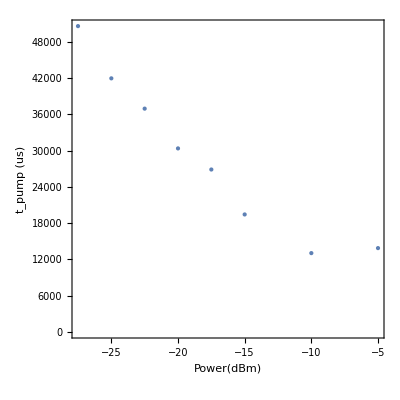

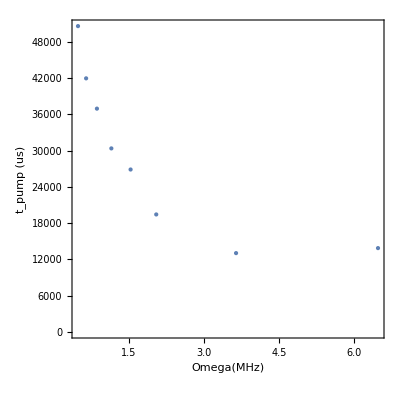

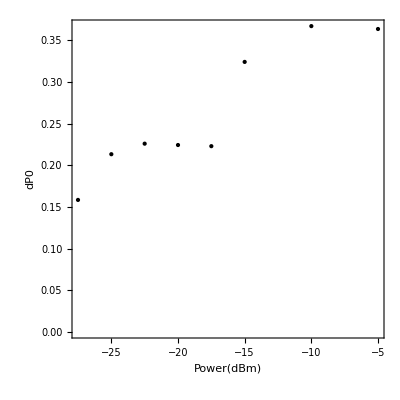

{G10→2.4495×10^-6,G21→0.0000214445}

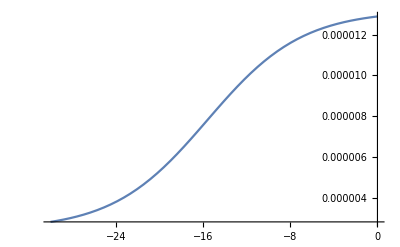

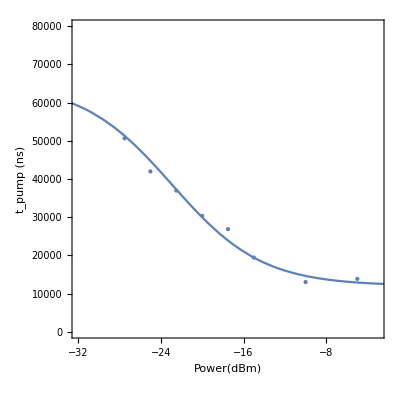

64974.5

7421.71

2.4495×10^-6

0.0000214445

124.885

```mathematica
pump=1/(2*Pi*Tpump);
Gpump=1/(2*Pi*Tpump);

dP=0.536*(Abs[Amp]/(Bs+Amp))
(*a=0.0003454;*)
a=0.000419;
G20=0.0026781;
Omega=Sqrt[a*10^((power-5)/10)]
ListPlot[Transpose@{power,Tpump},PlotStyle->PointSize[Large],PlotRange->All,LabelStyle->Large,AspectRatio->1, Frame->True,FrameLabel->{"Power(dBm)","t_pump (us)"}]
ListPlot[Transpose@{Omega*1000,Tpump},PlotStyle->PointSize[Large],PlotRange->All,LabelStyle->Large,AspectRatio->1, Frame->True,FrameLabel->{"Omega(MHz)","t_pump (us)"}]
ListPlot[Transpose@{power,dP},PlotStyle->{Black,PointSize[Large]},PlotRange->All,LabelStyle->Large, AspectRatio->1,Frame->True,FrameLabel->{"Power(dBm)","dP0"}]
Gfit=FindFit[Transpose[{power,Gpump}],G10+(G21*(a*10^((p-5)/10))/((G20+G21)^2+2*(a*10^((p-5)/10)))),{{G10,2*10^-6},{G21,0.00002}},p]
Plot[(G10+(G21*(a*10^((p-5)/10))/((G20+G21)^2+2*(a*10^((p-5)/10)))))/.Gfit,{p,-30,0}, PlotRange->All]
Show[ListPlot[Transpose@{power,Tpump},PlotStyle->PointSize[Large],PlotRange->{{-32,-3},{10,80000}},LabelStyle->Large,AspectRatio->1, Frame->True,FrameLabel->{"Power(dBm)","t_pump (ns)"}],Plot[1/(2*Pi*(G10+(G21*(a*10^((p-5)/10))/((G20+G21)^2+2*(a*10^((p-5)/10))))))/.Gfit,{p,-50,0}, PlotRange->All]]
1/(2*Pi*G10)/.Gfit
1/(2*Pi*G21)/.Gfit
G10/.Gfit
G21/.Gfit
G20/G21/.Gfit
```

{G21→0.000021448}

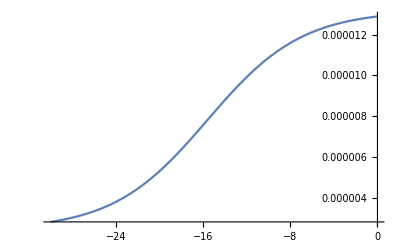

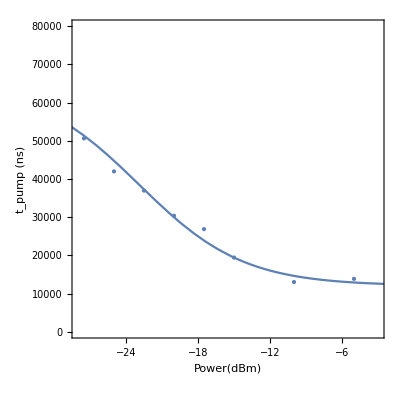

7420.52

0.000021448

124.865

```mathematica
Clear[G21,p];
a=0.000419;
G20=0.0026781;
T1fix=65000;
G10fix=1/(2*Pi*T1fix);
Gfit2=FindFit[Transpose[{power,Gpump}],G10fix+(G21*(a*10^((p-5)/10))/((G20+G21)^2+2*(a*10^((p-5)/10)))),{{G21,0.0005}},p]
Plot[(G10fix+(G21*(a*10^((p-5)/10))/((G20+G21)^2+2*(a*10^((p-5)/10)))))/.Gfit2,{p,-30,0}, PlotRange->All]
Show[ListPlot[Transpose@{power,Tpump},PlotStyle->PointSize[Large],PlotRange->{{-28,-3},{0,80000}},LabelStyle->Large,AspectRatio->1, Frame->True,FrameLabel->{"Power(dBm)","t_pump (ns)"}],Plot[1/(2*Pi*(G10fix+(G21*(a*10^((p-5)/10))/((G20+G21)^2+2*(a*10^((p-5)/10))))))/.Gfit2,{p,-50,0}, PlotRange->All]]
1/(2*Pi*G21)/.Gfit2
G21/.Gfit2
G20/G21/.Gfit2
```

{{{-27.5,50.6341},ErrorBar[8.38995]},{{-25,41.9846},ErrorBar[8.12187]},{{-22.5,36.9689},ErrorBar[6.67036]},{{-20,30.384},ErrorBar[10.7991]},{{-17.5,26.8888},ErrorBar[2.5486]},{{-15,19.4469},ErrorBar[5.18543]},{{-10,13.0439},ErrorBar[6.89238]},{{-5,13.8742},ErrorBar[1.49805]}}

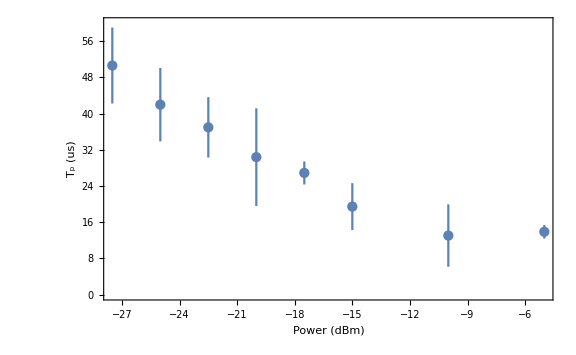

```mathematica
Needs["ErrorBarPlots`"]
AveTptable=Table[{{power[[i]],(Tpump[[i]]/1000)},ErrorBar[σTpump[[i]]/1000]},{i,1,8}]

plotTbAve=ErrorListPlot[AveTptable,ImageSize->Large,Frame->True,FrameStyle->Thick,FrameLabel->{"Power (dBm)","T_p (us)"},LabelStyle->{FontSize->20,Bold},Axes->False,PlotRange->{0,60},PlotStyle->colors,PlotLegends->PointLegend[colors,{"Tpump ave"},LegendMarkerSize->30]]
(*Show[plotTbAve,Plot[1/(1000*2*Pi*(G10fix+(G21*(a*10^((p-5)/10))/((G20+G21)^2+2*(a*10^((p-5)/10))))))/.Gfit2,{p,-50,0}, PlotRange->All]]*)
```

{G21→0.0000214454}

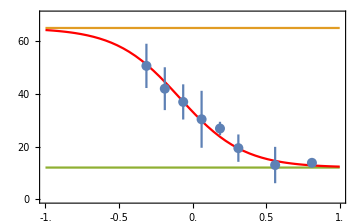

7421.41

0.0000214454

7.42141

124.88

```mathematica
Needs["ErrorBarPlots`"]
T1fix=65000;
G10fix=1/(2*Pi*T1fix);
Gfit2=FindFit[Transpose[{power,Gpump}][[2;;]],G10fix+(G21*(a*10^((p-5)/10))/((G20+G21)^2+2*(a*10^((p-5)/10)))),{{G21,0.0005}},p]
toplotT=Table[{{Log10[10^3 Omega[[i]]],10^-3 Tpump[[i]]},ErrorBar[10^-3 σTpump[[i]]]},{i,1,Length@power}];
branching=Show[Plot[{10^-3 T1fix,10^-3 T1fix,10^-3/(π G21+2π G10fix)/.Gfit2},{x,-1,1}, PlotRange->All,PlotStyle->{None,Automatic,Automatic}],Plot[10^-3/(2*Pi*(G10fix+(G21*10^(2(x-3)))/(G20^2+2 10^(2(x-3)))))/.Gfit2,{x,-1,1}, PlotRange->All,PlotStyle->Red],
ErrorListPlot[toplotT[[1;;]],PlotStyle->PointSize[0.02]],PlotRange->{0,70},Frame->True,FrameTicks->{{Table[0+20i,{i,0,4}],None},{Table[-1+0.5i,{i,0,4}],None}},ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]
1/(2*Pi*G21)/.Gfit2
G21/.Gfit2
10^-3/(2π G21)/.Gfit2
G20/G21/.Gfit2
```

```mathematica
Export["branching.eps",branching]
```

branching.eps

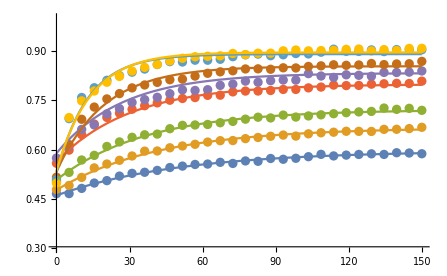

```mathematica
data={Averaged27p5,Averaged25,Averaged22p5,Averaged20,Averaged17p5,Averaged15,Averaged10,Averaged5};
Show[ListPlot[Transpose@{10^-3 delays[[;;Length@#]],#}&/@data,PlotRange->{0.3,1},PlotStyle->PointSize[0.015]],
Plot[Evaluate@Table[Amp[[i]]Exp[-1000t/Tpump[[i]]]+Bs[[i]],{i,1,Length@Tpump}],{t,0,150},PlotRange->All]]
```

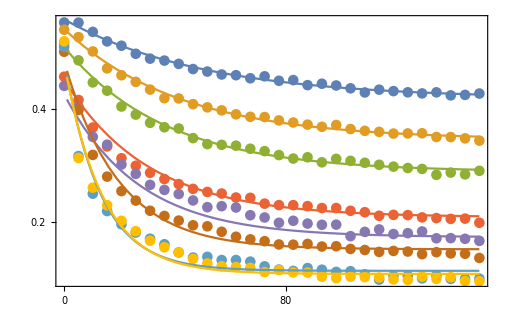

```mathematica
pth=0.56;
rth=Amp[[1]]+Bs[[1]];
Const=(1-rth)/(2pth);
p0[r_]:=(1-r)/(2Const)
Show[ListPlot[Transpose@{10^-3 delays[[;;Length@#]],#}&/@p0[data[[;;-1]]],PlotRange->{0.8,0},PlotStyle->PointSize[0.015]],
Plot[Evaluate@Table[p0[Amp[[i]]Exp[-1000t/Tpump[[i]]]+Bs[[i]]],{i,1,Length@Tpump}],{t,1,150},PlotRange->All],Frame->True,FrameTicks->{{Table[0.2i,{i,0,5}],None},{Table[40i,{i,0,10}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
```

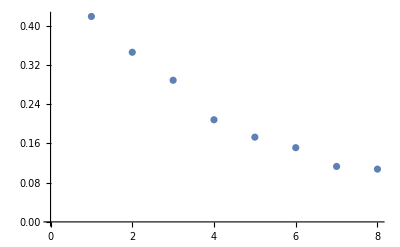

```mathematica
ListPlot[p0[Bs]]
```